```mathematica
<<StandardPolyLib`
```

```mathematica
SetDirectory["/Users/Admin/Dropbox/ThesisDropbox/GranSim2/source/"]
```

/Users/Admin/Dropbox/ThesisDropBox/GranSim2/source

```mathematica
dir = "/Users/Admin/Dropbox/ThesisDropbox/GranSim2/source/environment/build_environment/"

polygonDir[x_]:= dir<>"simulation_env/simulation_obj/particle_"<>ToString[x]<>".dat"
rcurrentDir[fileN_]:=dir<>"Rcurrent/Rcurrent"<>ToString[fileN]<>".dat"
boxDir=dir<>"simulation_env/simulation_box/container.dat";
simstepDir[fileN_]:=dir<>"Rcurrent/Rsimstep"<>ToString[fileN]<>".dat";


box= Import[boxDir,"Table"];

(*rand=Import[dir<>"Rcurrent/RandomRolls.dat","Table"];*)
```

/Users/Admin/Dropbox/ThesisDropbox/GranSim2/source/environment/build_environment/

```mathematica
nfiles=1060;

Rcurrent = Table[Import[rcurrentDir[x],"Table"],{x,100,nfiles}];

{{simstep,growthRate,overlap}} = Import[dir<>"Rcurrent/Rsimstep100.dat","Table"]
simstep= Table[ Import[simstepDir[x],"Table"],{x,100,nfiles}];
simstep=simstep[[;;,1,1]];
numPolys=Max[Rcurrent[[1,;;,4]]  ];
polys=Table[{},{x,1,numPolys }];
polys=Table[Import[polygonDir[x], "Table"],{x,1,numPolys }];
```

{{100,0.0001,0}}

```mathematica
simstep[[1]]//MatrixForm
```

100

```mathematica
simN=110;
ani=Table[
If[ Rcurrent[[simN]]==Rcurrent[[simN-1]],Null,
pt=Table[
DeleteCases[If[Rcurrent[[simN,#,4]]==x,#]&/@Range[Length[Rcurrent[[simN]]]],Null],{x,1,Length[polys]}];


inf=Flatten[Table[Inflate[Rcurrent[[simN,#,1;;3]]&/@pt[[x]], polys[[x]], simstep[[simN]],growthRate  ,1],{x,1,Length[pt]}],1];


(*Rasterize[*)
Show[{Graphics[{White,Polygon[1.2StandardPolygon[6]]}],PolydisperseFinalConfiguration[Rcurrent[[simN]],polys,simstep[[simN]],growthRate, box],
Show@Table[Render[inf[[x]],colF[Rcurrent[[simN,x,4]]]],{x,Range@Length@Rcurrent[[simN,;;,4]]}]
(*ListPlot[inf,Joined->True,Axes->True]*)}]
(*,RasterSize->600]*)
]
,{simN,2,nfiles-100}];

(*r=DelaunayMesh[Rcurrent[[;;,1;;2]]];
delPoints=MeshCoordinates[r];


Show[{
ob,
(*ListPlot[rand+ Table[Rcurrent[[1,1;;2]],{x,1,Length[rand]}],PlotStyle->PointSize[Small]],*)
Graphics[Point[delPoints]],
Graphics[Line[box]]
}]*)
```

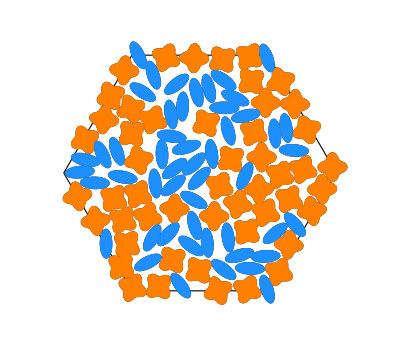

959

244

294

```mathematica
lastframe=ani[[-1]]
NoNullAni=DeleteCases[ani,Null];
Length[ani]
Length[NoNullAni]
Do[AppendTo[NoNullAni,lastframe],{x,1,50}];
Length[NoNullAni]
```

```mathematica
AbsoluteTiming[Export["/Users/Admin/Thesis/Plotting Tools/Animated_Plots/Morphologies/Morphologies_Simulation.gif",ani];]
AbsoluteTiming[Export["/Users/Admin/Thesis/Plotting Tools/Animated_Plots/Morphologies/Morphologies_Simulation.mov",ani];]
```

{88.20589,Null}

{149.84966,Null}

```mathematica
AbsoluteTiming[Export["/Users/Admin/Thesis/Plotting Tools/Animated_Plots/Morphologies/Morphologies_Simulation.gif",NoNullAni];]
(*AbsoluteTiming[Export["/Users/Admin/Thesis/Plotting Tools/Animated_Plots/Morphologies/Morphologies_Simulation.mov",ani];]*)
```

{34.09629,Null}

```mathematica
ani[[1;;10]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Rcurrent[[1]]==Rcurrent[[2]]
```

True